## Interpolation

InterpolatingFunction[…]

-Graphics3D-

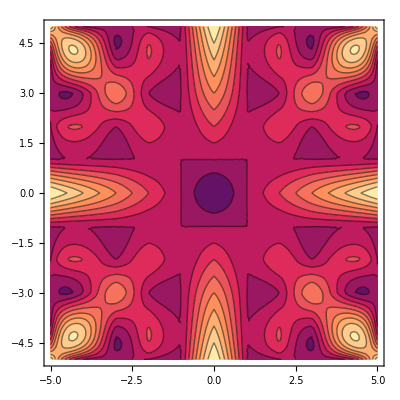

```mathematica
Flatten[Table[{{x,y},GCD[x,y]},{x,-5,5},{y,-5,5}],1];
f=Interpolation[%]
Plot3D[f[x,y],{x,-5,5},{y,-5,5}]
ContourPlot[f[x,y],{x,-5,5},{y,-5,5}]
```

InterpolatingFunction[…]

-Graphics3D-

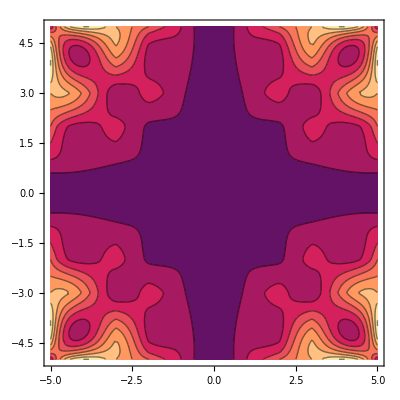

```mathematica
Flatten[Table[{{x,y},LCM[x,y]},{x,-5,5},{y,-5,5}],1];
f=Interpolation[%]
Plot3D[f[x,y],{x,-5,5},{y,-5,5}]
ContourPlot[f[x,y],{x,-5,5},{y,-5,5}]
```

InterpolatingFunction[…]

-Graphics3D-

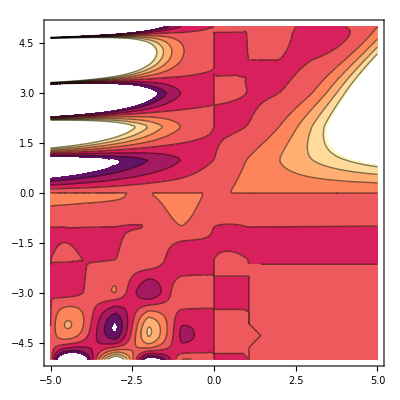

```mathematica
Flatten[Table[{{x,y},Binomial[x,y]},{x,-5,5},{y,-5,5}],1];
f=Interpolation[%]
Plot3D[f[x,y],{x,-5,5},{y,-5,5}]
ContourPlot[f[x,y],{x,-5,5},{y,-5,5}]
```

InterpolatingFunction[…]

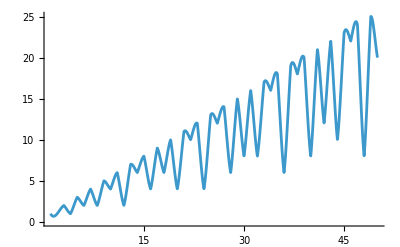

```mathematica
Flatten[Table[{x,EulerPhi[x]},{x,1,50}],1];
f=Interpolation[%]
Plot[f[x],{x,1,50}]
```